```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,25000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[1,0.0001,0.5,0,7]
```

2.

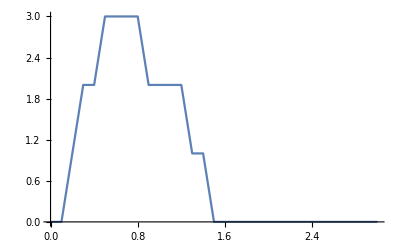

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,0.5,0,7]},{ω,Range[-4,4,0.01]}]]
```

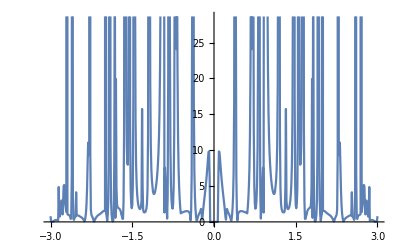

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1.5,0,0,15]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
Δ[ω_,m_,N_]:=Δ[ω,m,N]=Abs[Mean[Table[tr[ω,0.0001,1,0,1,m],N+100]]-Mean[Table[tr[ω,0.0001,1,0,1,m],N]]]
```

```mathematica
υ[ϵ1_,x_,y_]:=Module[{μ1=RandomInteger[{1,7}], μ2=RandomInteger[{1,7}], μ3=RandomInteger[{1,7}], μ4=RandomInteger[{1,7}],μ5=RandomInteger[{8,14}], μ6=RandomInteger[{8,14}], μ7=RandomInteger[{8,14}],μ8=RandomInteger[{8,14}]
(*Print[{μ1,μ2,μ3,μ5,μ6,μ8}]*)},
η5:=Module[{g:=Inverse[β[ω,0.001,1,0,7]]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0,7]},ReplacePart[gg,{{μ1,μ1},{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0,7]},ReplacePart[gg,{{μ2,μ2},{μ6,μ6}}->ω+ⅈ*0.001-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0,7]},ReplacePart[gg,{{μ3,μ3},{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0,7]},ReplacePart[gg,{{μ4,μ4},{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[14]-imp1.ConjugateTranspose[T1[1,7]].SR[ω,0.001,1,0,7].T1[1,7]].imp1;Sl12:=Inverse[IdentityMatrix[14]-imp2.ConjugateTranspose[T1[1,7]].Sl11.T1[1,7]].imp2;Sl13:=Inverse[IdentityMatrix[14]-imp3.ConjugateTranspose[T1[1,7]].Sl12.T1[1,7]].imp3;Sl14:=Inverse[IdentityMatrix[14]-imp4.ConjugateTranspose[T1[1,7]].Sl13.T1[1,7]].imp4;Il1:=Inverse[IdentityMatrix[14]-Sl14.ρ[1,7].SR[ω,0.001,1,0,7].ρ[1,7]].Sl14;Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.001,1,0,7].ρ[1,7].Sl14.ρ[1,7]].SR[ω,0.001,1,0,7];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0,7].ρ[1,7].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.ρ[1,7].grr1.ρ[1,7]-ρ[1,7].GNON1.ρ[1,7].GNON1]]];Clear[m5];m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];
ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/2imp/2imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/3imp/3imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/4imp/4imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/5imp/5imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/6imp/6imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/7imp/7imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/8imp/8imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/9imp/9imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/10imp/10imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/11imp/11imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/transmission/12imp/12imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/(x*100)];
list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11},{12,ρ12}};Print[list];{list[[Position[list,Min[list]][[1,1]],1]],Min[list],Show[ListLinePlot[m5,PlotStyle->Red],%12],
{μ1,μ3,μ5,μ8,μ2,μ4,μ6,μ7},μ1+μ3+μ5+μ8+μ2+μ4+μ6+μ7}]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m],u1=RandomInteger[{1,14}],u2=RandomInteger[{8,14}]},ReplacePart[κ,{{u1,u1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m],u1=RandomInteger[{1,4}],u2=RandomInteger[{5,9}],u3=RandomInteger[{10,14}]},ReplacePart[κ,{{u1,u1},{u2,u2},{u3,u3}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_,m_,num_]:=RandomSample[Join[Table[imp1[ω,δ,t,ϵ,ϵ1,m],num],Table[imp2[ω,δ,t,ϵ,0,m],100-num]],100]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_,num_]:=Module[{gg=g[ω,δ,t,ϵ,m],x=T1[1,m],T=ρ[1,m]},
η=Module[{c=RandomSample[Join[Table[imp1[ω,δ,t,ϵ,ϵ1,m],num],Table[imp2[ω,δ,t,ϵ,0,m],100-num]],100]},
sl1= Module[{J=SL[ω,δ,t,ϵ,m]},Do[J=Inverse[IdentityMatrix[14]-c[[κ]].ConjugateTranspose[x].J.x].c[[κ]],{κ,1,100}]; J=J];
Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,δ,t,0,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0,m].T.sl1.T].SR[ω,δ,1,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
η]
```

```mathematica
Mean[Table[tr1[1.5,0.0001,1,0,0.7,7,100],5000]]
```

0.303651

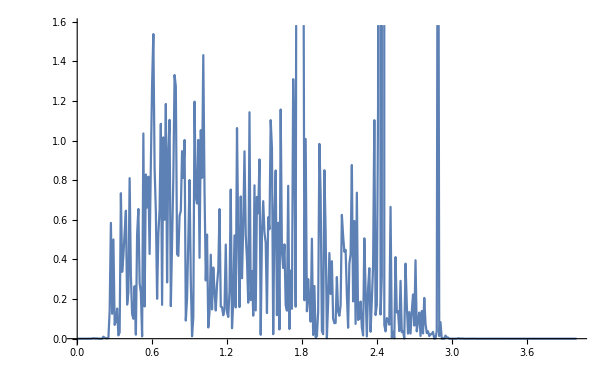

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.0001,1,0,0.5,7,100]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.5,7,100],4000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000404565},{0.01,0.0000262433},{0.02,0.0000219141},{0.03,0.0000272746},{0.04,0.0000399808},{0.05,0.0000648081},{0.06,0.000099425},{0.07,0.000139572},{0.08,0.00019413},{0.09,0.000264958},{0.1,0.000365734},{0.11,0.000471692},{0.12,0.000600934},{0.13,0.000771609},{0.14,0.000968882},{0.15,0.00127728},{0.16,0.00162986},{0.17,0.00206313},{0.18,0.00270909},{0.19,0.00371965},{0.2,0.00503349},{0.21,0.00734064},{0.22,0.0116639},{0.23,0.0222007},{0.24,0.0524545},{0.25,0.0629448},{0.26,0.084832},{0.27,0.16298},{0.28,0.253598},{0.29,0.31669},{0.3,0.350685},{0.31,0.372018},{0.32,0.392797},{0.33,0.404489},{0.34,0.411547},{0.35,0.420149},{0.36,0.418169},{0.37,0.416799},{0.38,0.417567},{0.39,0.410192},{0.4,0.408165},{0.41,0.410656},{0.42,0.529261},{0.43,0.56477},{0.44,0.725554},{0.45,0.890852},{0.46,0.724482},{0.47,0.630002},{0.48,0.564845},{0.49,0.553464},{0.5,0.528763},{0.51,0.531944},{0.52,0.54559},{0.53,0.556248},{0.54,0.568158},{0.55,0.582719},{0.56,0.594082},{0.57,0.619412},{0.58,0.631888},{0.59,0.642314},{0.6,0.679179},{0.61,0.691329},{0.62,0.692844},{0.63,0.699205},{0.64,0.73029},{0.65,0.732937},{0.66,0.746806},{0.67,0.761798},{0.68,0.76578},{0.69,0.776121},{0.7,0.777035},{0.71,0.797526},{0.72,0.799392},{0.73,0.80543},{0.74,0.840367},{0.75,0.82092},{0.76,0.833677},{0.77,0.807975},{0.78,0.856178},{0.79,0.853035},{0.8,0.88229},{0.81,0.838081},{0.82,0.830535},{0.83,0.80443},{0.84,0.750657},{0.85,0.709824},{0.86,0.688346},{0.87,0.783345},{0.88,0.941628},{0.89,0.757189},{0.9,0.703841},{0.91,0.611315},{0.92,0.576362},{0.93,0.586351},{0.94,0.615461},{0.95,0.651677},{0.96,0.700879},{0.97,0.747055},{0.98,0.822567},{0.99,0.872777},{1.,0.933556},{1.01,1.03971},{1.02,0.952002},{1.03,0.7302},{1.04,0.44137},{1.05,0.358931},{1.06,0.351165},{1.07,0.368215},{1.08,0.359379},{1.09,0.341584},{1.1,0.331502},{1.11,0.342425},{1.12,0.349037},{1.13,0.346734},{1.14,0.340139},{1.15,0.363476},{1.16,0.37733},{1.17,0.390808},{1.18,0.410293},{1.19,0.414763},{1.2,0.430145},{1.21,0.441617},{1.22,0.464687},{1.23,0.466438},{1.24,0.450888},{1.25,0.476217},{1.26,0.495177},{1.27,0.488574},{1.28,0.482246},{1.29,0.463048},{1.3,0.492231},{1.31,0.496172},{1.32,0.485394},{1.33,0.502167},{1.34,0.468835},{1.35,0.510334},{1.36,0.507484},{1.37,0.513569},{1.38,0.512118},{1.39,0.482787},{1.4,0.490489},{1.41,0.488689},{1.42,0.479323},{1.43,0.483532},{1.44,0.465142},{1.45,0.455527},{1.46,0.46453},{1.47,0.472327},{1.48,0.460417},{1.49,0.468149},{1.5,0.455533},{1.51,0.448602},{1.52,0.450448},{1.53,0.443437},{1.54,0.421557},{1.55,0.417826},{1.56,0.415482},{1.57,0.405067},{1.58,0.404617},{1.59,0.414469},{1.6,0.404798},{1.61,0.409468},{1.62,0.409845},{1.63,0.400172},{1.64,0.395917},{1.65,0.403028},{1.66,0.432376},{1.67,0.487989},{1.68,0.495514},{1.69,0.474921},{1.7,0.620525},{1.71,0.618296},{1.72,0.848699},{1.73,0.924185},{1.74,1.08784},{1.75,1.65925},{1.76,2.91936},{1.77,7.72039},{1.78,7.21013},{1.79,5.29761},{1.8,3.31625},{1.81,2.37194},{1.82,1.01043},{1.83,0.554491},{1.84,0.361982},{1.85,0.32152},{1.86,0.332642},{1.87,0.360117},{1.88,0.379877},{1.89,0.405451},{1.9,0.421514},{1.91,0.431256},{1.92,0.44008},{1.93,0.440536},{1.94,0.461578},{1.95,0.470131},{1.96,0.47327},{1.97,0.458701},{1.98,0.450261},{1.99,0.466297},{2.,0.479081},{2.01,0.46909},{2.02,0.457094},{2.03,0.456429},{2.04,0.471422},{2.05,0.459545},{2.06,0.468995},{2.07,0.463356},{2.08,0.440756},{2.09,0.446104},{2.1,0.424922},{2.11,0.421465},{2.12,0.417875},{2.13,0.416187},{2.14,0.413415},{2.15,0.408713},{2.16,0.411172},{2.17,0.40177},{2.18,0.390112},{2.19,0.380135},{2.2,0.359678},{2.21,0.371856},{2.22,0.349121},{2.23,0.343775},{2.24,0.344517},{2.25,0.327607},{2.26,0.319476},{2.27,0.320369},{2.28,0.311628},{2.29,0.302322},{2.3,0.299967},{2.31,0.297298},{2.32,0.283852},{2.33,0.28036},{2.34,0.28541},{2.35,0.277264},{2.36,0.301011},{2.37,0.321403},{2.38,0.371497},{2.39,0.460894},{2.4,0.62835},{2.41,1.20352},{2.42,4.1411},{2.43,3.73197},{2.44,2.90425},{2.45,1.87743},{2.46,1.04497},{2.47,0.557147},{2.48,0.300674},{2.49,0.207201},{2.5,0.184501},{2.51,0.191582},{2.52,0.193855},{2.53,0.207812},{2.54,0.208514},{2.55,0.212016},{2.56,0.214596},{2.57,0.222237},{2.58,0.222355},{2.59,0.22796},{2.6,0.220821},{2.61,0.21725},{2.62,0.219721},{2.63,0.225462},{2.64,0.225757},{2.65,0.222536},{2.66,0.218512},{2.67,0.220686},{2.68,0.215816},{2.69,0.222418},{2.7,0.215193},{2.71,0.209712},{2.72,0.211453},{2.73,0.194449},{2.74,0.197948},{2.75,0.189485},{2.76,0.188376},{2.77,0.182419},{2.78,0.176972},{2.79,0.172296},{2.8,0.165556},{2.81,0.159308},{2.82,0.154516},{2.83,0.151779},{2.84,0.171707},{2.85,2.78838},{2.86,3.37155},{2.87,2.55798},{2.88,1.72084},{2.89,0.388583},{2.9,0.0980199},{2.91,0.0226371},{2.92,0.00703672},{2.93,0.0048965},{2.94,0.00334891},{2.95,0.00275516},{2.96,0.00207086},{2.97,0.00170451},{2.98,0.00140212},{2.99,0.00116412},{3.,0.000975816},{3.01,0.000829693},{3.02,0.000710254},{3.03,0.000606505},{3.04,0.0005361},{3.05,0.000465666},{3.06,0.000400058},{3.07,0.000347824},{3.08,0.000298914},{3.09,0.000281335},{3.1,0.000253814},{3.11,0.000224848},{3.12,0.000193371},{3.13,0.000180475},{3.14,0.000174142},{3.15,0.00014916},{3.16,0.000133086},{3.17,0.000114857},{3.18,0.000112572},{3.19,0.000101464},{3.2,0.0000918701},{3.21,0.0000886442},{3.22,0.000078002},{3.23,0.000069913},{3.24,0.0000689286},{3.25,0.0000613246},{3.26,0.0000578544},{3.27,0.0000514032},{3.28,0.0000501922},{3.29,0.0000484219},{3.3,0.0000414397},{3.31,0.0000393307},{3.32,0.0000372077},{3.33,0.0000335552},{3.34,0.0000328162},{3.35,0.0000289241},{3.36,0.0000268798},{3.37,0.0000257171},{3.38,0.0000236905},{3.39,0.000022603},{3.4,0.0000206944},{3.41,0.0000196309},{3.42,0.0000194421},{3.43,0.0000177235},{3.44,0.0000165303},{3.45,0.00001516},{3.46,0.0000147332},{3.47,0.0000143989},{3.48,0.0000131864},{3.49,0.0000125367},{3.5,0.0000111268},{3.51,0.0000113751},{3.52,0.0000104743},{3.53,9.65645×10^-6},{3.54,9.36872×10^-6},{3.55,8.6865×10^-6},{3.56,8.4624×10^-6},{3.57,8.26613×10^-6},{3.58,7.24042×10^-6},{3.59,7.52929×10^-6},{3.6,6.50369×10^-6},{3.61,6.46704×10^-6},{3.62,6.57022×10^-6},{3.63,5.78401×10^-6},{3.64,5.77166×10^-6},{3.65,5.37968×10^-6},{3.66,4.8455×10^-6},{3.67,4.61179×10^-6},{3.68,4.61883×10^-6},{3.69,4.222×10^-6},{3.7,4.07502×10^-6},{3.71,3.80207×10^-6},{3.72,3.77369×10^-6},{3.73,3.72209×10^-6},{3.74,3.41223×10^-6},{3.75,3.42766×10^-6},{3.76,3.26001×10^-6},{3.77,3.00021×10^-6},{3.78,2.82522×10^-6},{3.79,2.81477×10^-6},{3.8,2.64031×10^-6},{3.81,2.39558×10^-6},{3.82,2.4363×10^-6},{3.83,2.32449×10^-6},{3.84,2.26413×10^-6},{3.85,2.16401×10^-6},{3.86,2.10532×10^-6},{3.87,1.87125×10^-6},{3.88,1.92627×10^-6},{3.89,1.81365×10^-6},{3.9,1.69682×10^-6},{3.91,1.66644×10^-6},{3.92,1.55932×10^-6},{3.93,1.48964×10^-6},{3.94,1.38654×10^-6},{3.95,1.34131×10^-6},{3.96,1.4435×10^-6},{3.97,1.27532×10^-6},{3.98,1.28231×10^-6},{3.99,1.19327×10^-6},{4.,1.10087×10^-6}}

```mathematica
Table[Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.5,7,num],4000]]},{ω,Range[0,4,0.01]}],{num,Range[10,100,10]}]
```

{{{0.,4.03749×10^-7},{0.01,7.37372×10^-7},{0.02,1.96152×10^-6},{0.03,3.56851×10^-6},{0.04,6.53543×10^-6},{0.05,0.0000107083},{0.06,0.0000154629},{0.07,0.0000232422},{0.08,0.0000305861},{0.09,0.0000418859},{0.1,0.0000525865},{0.11,0.000068226},{0.12,0.0000940059},{0.13,0.000107873},{0.14,0.000146592},{0.15,0.000175871},{0.16,0.000230329},{0.17,0.000297017},365,{3.83,1.94582×10^-7},{3.84,2.58433×10^-7},{3.85,1.91935×10^-7},{3.86,2.43534×10^-7},{3.87,2.25687×10^-7},{3.88,2.19372×10^-7},{3.89,1.69053×10^-7},{3.9,1.45876×10^-7},{3.91,1.89595×10^-7},{3.92,1.58149×10^-7},{3.93,1.75354×10^-7},{3.94,1.88661×10^-7},{3.95,1.59378×10^-7},{3.96,1.3098×10^-7},{3.97,1.46815×10^-7},{3.98,1.07721×10^-7},{3.99,1.24175×10^-7},{4.,1.30488×10^-7}},8,{1}}
 |  |  |  |

```mathematica
Export["110imp100.csv",%262[[11]]]
```

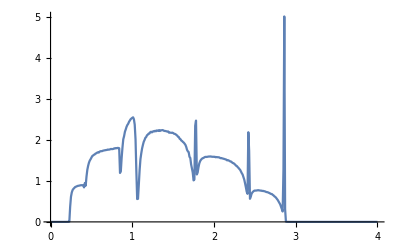

```mathematica
ListPlot[%263,Joined->True]
```

```mathematica
Table[{num,Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.5,7,num],4000]]},{ω,Range[0,4,0.01]}]},{num,Range[20,21,1]}]
```

{{20,{{0.,1.49592×10^-6},{0.01,1.35869×10^-6},{0.02,3.41496×10^-6},{0.03,7.13861×10^-6},{0.04,0.0000136233},{0.05,0.0000182079},{0.06,0.0000276354},{0.07,0.0000418886},{0.08,0.0000618113},{0.09,0.0000765041},{0.1,0.000100741},{0.11,0.000119887},{0.12,0.000167008},{0.13,0.000206693},{0.14,0.000264809},{0.15,0.000314821},{0.16,0.000451151},{0.17,0.000563258},{0.18,0.000769162},{0.19,0.00100654},{0.2,0.00144401},{0.21,0.00246907},{0.22,0.00405744},{0.23,0.0110161},{0.24,0.184789},{0.25,0.40071},{0.26,0.537029},{0.27,0.624927},{0.28,0.673681},{0.29,0.707957},{0.3,0.728905},{0.31,0.751401},{0.32,0.763534},{0.33,0.777081},{0.34,0.78964},{0.35,0.798679},{0.36,0.806803},{0.37,0.807233},{0.38,0.808337},{0.39,0.808003},{0.4,0.797495},{0.41,0.722198},{0.42,1.09333},{0.43,0.801999},{0.44,0.771264},{0.45,0.882119},{0.46,0.978369},{0.47,1.07742},{0.48,1.15695},{0.49,1.20754},{0.5,1.26572},{0.51,1.30642},{0.52,1.33091},{0.53,1.35224},{0.54,1.37506},{0.55,1.42276},{0.56,1.43084},{0.57,1.45352},{0.58,1.45769},{0.59,1.4648},{0.6,1.48378},{0.61,1.51042},{0.62,1.50925},{0.63,1.51752},{0.64,1.5374},{0.65,1.53357},{0.66,1.54651},{0.67,1.55509},{0.68,1.55794},{0.69,1.57136},{0.7,1.56177},{0.71,1.57419},{0.72,1.5747},{0.73,1.58106},{0.74,1.6009},{0.75,1.59505},{0.76,1.6034},{0.77,1.61114},{0.78,1.6188},{0.79,1.61982},{0.8,1.63607},{0.81,1.63424},{0.82,1.63489},{0.83,1.63511},{0.84,1.60762},{0.85,1.04825},{0.86,0.953516},{0.87,0.983703},{0.88,1.19007},{0.89,1.38813},{0.9,1.52737},{0.91,1.6598},{0.92,1.76343},{0.93,1.8491},{0.94,1.91354},{0.95,1.96226},{0.96,2.02131},{0.97,2.08449},{0.98,2.13371},{0.99,2.15979},{1.,2.19146},{1.01,2.22112},{1.02,2.1533},{1.03,1.94552},{1.04,1.45859},{1.05,0.66624},{1.06,0.33405},{1.07,0.333642},{1.08,0.452549},{1.09,0.665867},{1.1,0.898019},{1.11,1.04902},{1.12,1.19148},{1.13,1.29795},{1.14,1.37255},{1.15,1.43825},{1.16,1.51332},{1.17,1.5387},{1.18,1.59525},{1.19,1.60726},{1.2,1.64699},{1.21,1.6706},{1.22,1.69599},{1.23,1.71268},{1.24,1.68607},{1.25,1.71678},{1.26,1.7353},{1.27,1.72214},{1.28,1.7329},{1.29,1.72369},{1.3,1.74591},{1.31,1.75258},{1.32,1.73688},{1.33,1.75858},{1.34,1.72647},{1.35,1.76904},{1.36,1.7678},{1.37,1.76617},{1.38,1.76387},{1.39,1.73111},{1.4,1.73842},{1.41,1.74265},{1.42,1.71069},{1.43,1.72575},{1.44,1.73004},{1.45,1.68904},{1.46,1.6795},{1.47,1.69291},{1.48,1.7003},{1.49,1.69159},{1.5,1.68141},{1.51,1.66481},{1.52,1.64959},{1.53,1.63923},{1.54,1.63093},{1.55,1.60425},{1.56,1.57008},{1.57,1.5458},{1.58,1.5153},{1.59,1.48461},{1.6,1.45559},{1.61,1.4339},{1.62,1.42519},{1.63,1.39975},{1.64,1.37228},{1.65,1.3413},{1.66,1.27409},{1.67,1.19558},{1.68,1.15321},{1.69,1.14793},{1.7,1.00801},{1.71,0.982735},{1.72,0.852526},{1.73,0.797238},{1.74,0.751814},{1.75,0.773647},{1.76,1.23997},{1.77,3.73416},{1.78,3.46034},{1.79,1.46353},{1.8,0.894854},{1.81,0.926744},{1.82,1.04215},{1.83,1.11335},{1.84,1.18104},{1.85,1.22638},{1.86,1.24933},{1.87,1.25819},{1.88,1.2822},{1.89,1.29496},{1.9,1.29938},{1.91,1.31333},{1.92,1.3159},{1.93,1.32044},{1.94,1.32299},{1.95,1.32376},{1.96,1.32534},{1.97,1.31074},{1.98,1.31423},{1.99,1.31944},{2.,1.31696},{2.01,1.31188},{2.02,1.30567},{2.03,1.3063},{2.04,1.29673},{2.05,1.29538},{2.06,1.29218},{2.07,1.28338},{2.08,1.26911},{2.09,1.26796},{2.1,1.26432},{2.11,1.25356},{2.12,1.25589},{2.13,1.24174},{2.14,1.23061},{2.15,1.21678},{2.16,1.22392},{2.17,1.20771},{2.18,1.1909},{2.19,1.18093},{2.2,1.1547},{2.21,1.15747},{2.22,1.14491},{2.23,1.11935},{2.24,1.116},{2.25,1.08174},{2.26,1.0704},{2.27,1.03993},{2.28,1.02632},{2.29,1.00921},{2.3,0.975894},{2.31,0.949021},{2.32,0.912441},{2.33,0.873303},{2.34,0.829677},{2.35,0.79764},{2.36,0.735455},{2.37,0.680419},{2.38,0.606468},{2.39,0.559645},{2.4,0.527663},{2.41,0.6994},{2.42,3.12796},{2.43,2.37616},{2.44,0.588329},{2.45,0.453519},{2.46,0.47883},{2.47,0.530162},{2.48,0.567988},{2.49,0.595557},{2.5,0.600772},{2.51,0.612921},{2.52,0.613383},{2.53,0.626485},{2.54,0.620662},{2.55,0.620322},{2.56,0.618225},{2.57,0.615473},{2.58,0.612737},{2.59,0.605796},{2.6,0.608352},{2.61,0.602551},{2.62,0.59385},{2.63,0.592756},{2.64,0.581151},{2.65,0.568082},{2.66,0.56324},{2.67,0.550567},{2.68,0.547967},{2.69,0.524593},{2.7,0.51918},{2.71,0.509891},{2.72,0.488323},{2.73,0.474795},{2.74,0.45621},{2.75,0.432668},{2.76,0.408503},{2.77,0.390128},{2.78,0.36974},{2.79,0.343649},{2.8,0.309465},{2.81,0.266494},{2.82,0.233971},{2.83,0.201311},{2.84,0.165807},{2.85,0.670159},{2.86,7.73521},{2.87,0.60039},{2.88,0.0710709},{2.89,0.00514757},{2.9,0.00264252},{2.91,0.00163359},{2.92,0.00116281},{2.93,0.000880521},{2.94,0.000625118},{2.95,0.000493144},{2.96,0.000397466},{2.97,0.00033953},{2.98,0.000264036},{2.99,0.000229903},{3.,0.000196898},{3.01,0.000137265},{3.02,0.000140091},{3.03,0.000128183},{3.04,0.000102607},{3.05,0.0000871087},{3.06,0.000084293},{3.07,0.0000681533},{3.08,0.0000759344},{3.09,0.0000511739},{3.1,0.0000452907},{3.11,0.0000467074},{3.12,0.0000363553},{3.13,0.0000374577},{3.14,0.000029417},{3.15,0.0000279075},{3.16,0.0000275558},{3.17,0.0000255664},{3.18,0.0000231604},{3.19,0.0000195745},{3.2,0.0000206082},{3.21,0.000016982},{3.22,0.0000143761},{3.23,0.0000152269},{3.24,0.0000138418},{3.25,0.0000123732},{3.26,0.0000114981},{3.27,0.0000103122},{3.28,0.0000103825},{3.29,7.78087×10^-6},{3.3,8.57724×10^-6},{3.31,7.91357×10^-6},{3.32,7.37058×10^-6},{3.33,7.175×10^-6},{3.34,6.64445×10^-6},{3.35,5.58383×10^-6},{3.36,5.79433×10^-6},{3.37,5.29393×10^-6},{3.38,4.38278×10^-6},{3.39,4.33854×10^-6},{3.4,3.71472×10^-6},{3.41,4.19827×10^-6},{3.42,3.63711×10^-6},{3.43,3.43325×10^-6},{3.44,3.27776×10^-6},{3.45,3.22177×10^-6},{3.46,2.78495×10^-6},{3.47,2.82116×10^-6},{3.48,2.54954×10^-6},{3.49,2.53529×10^-6},{3.5,2.35341×10^-6},{3.51,2.0968×10^-6},{3.52,1.95688×10^-6},{3.53,1.74975×10^-6},{3.54,1.87256×10^-6},{3.55,1.61669×10^-6},{3.56,1.61684×10^-6},{3.57,1.57807×10^-6},{3.58,1.29224×10^-6},{3.59,1.61472×10^-6},{3.6,1.282×10^-6},{3.61,1.41885×10^-6},{3.62,1.25186×10^-6},{3.63,1.26452×10^-6},{3.64,1.04621×10^-6},{3.65,1.07614×10^-6},{3.66,1.00132×10^-6},{3.67,8.91324×10^-7},{3.68,8.63679×10^-7},{3.69,9.55384×10^-7},{3.7,8.63586×10^-7},{3.71,7.51771×10^-7},{3.72,8.50568×10^-7},{3.73,6.98664×10^-7},{3.74,6.62351×10^-7},{3.75,6.70194×10^-7},{3.76,6.50853×10^-7},{3.77,5.63827×10^-7},{3.78,6.63987×10^-7},{3.79,5.5918×10^-7},{3.8,5.52393×10^-7},{3.81,5.21825×10^-7},{3.82,5.59058×10^-7},{3.83,4.55947×10^-7},{3.84,4.67188×10^-7},{3.85,4.13007×10^-7},{3.86,4.04248×10^-7},{3.87,3.84771×10^-7},{3.88,3.87632×10^-7},{3.89,3.9189×10^-7},{3.9,3.89846×10^-7},{3.91,3.20827×10^-7},{3.92,3.25619×10^-7},{3.93,3.11651×10^-7},{3.94,2.81193×10^-7},{3.95,2.59824×10^-7},{3.96,2.57391×10^-7},{3.97,2.69252×10^-7},{3.98,2.64768×10^-7},{3.99,2.63137×10^-7},{4.,2.11683×10^-7}}},{21,{{0.,1.79662×10^-6},{0.01,1.21524×10^-6},{0.02,3.39641×10^-6},{0.03,7.44972×10^-6},{0.04,0.0000131383},{0.05,0.0000201542},{0.06,0.0000292158},{0.07,0.0000436611},{0.08,0.0000616605},{0.09,0.0000776225},{0.1,0.000111904},{0.11,0.000132984},{0.12,0.000163644},{0.13,0.000222062},{0.14,0.000290619},{0.15,0.000369377},{0.16,0.000452088},{0.17,0.000580698},{0.18,0.000768511},{0.19,0.00111926},{0.2,0.00156314},{0.21,0.00236009},{0.22,0.00391403},{0.23,0.0109459},{0.24,0.170375},{0.25,0.375818},{0.26,0.522732},{0.27,0.610555},{0.28,0.665427},{0.29,0.695433},{0.3,0.717113},{0.31,0.741747},{0.32,0.756738},{0.33,0.773195},{0.34,0.782762},{0.35,0.787801},{0.36,0.796655},{0.37,0.800804},{0.38,0.804156},{0.39,0.799144},{0.4,0.786906},{0.41,0.711035},{0.42,1.11852},{0.43,0.798948},{0.44,0.767106},{0.45,0.84821},{0.46,0.945956},{0.47,1.04334},{0.48,1.12167},{0.49,1.16995},{0.5,1.23422},{0.51,1.28248},{0.52,1.30959},{0.53,1.3392},{0.54,1.35351},{0.55,1.39087},{0.56,1.40351},{0.57,1.43228},{0.58,1.45315},{0.59,1.44219},{0.6,1.4693},{0.61,1.4851},{0.62,1.48627},{0.63,1.49772},{0.64,1.51214},{0.65,1.50977},{0.66,1.5272},{0.67,1.5387},{0.68,1.53479},{0.69,1.54823},{0.7,1.54877},{0.71,1.55987},{0.72,1.55913},{0.73,1.57015},{0.74,1.58499},{0.75,1.57903},{0.76,1.58366},{0.77,1.58507},{0.78,1.60096},{0.79,1.60801},{0.8,1.62146},{0.81,1.6176},{0.82,1.6198},{0.83,1.61881},{0.84,1.59338},{0.85,1.05853},{0.86,0.951566},{0.87,0.976694},{0.88,1.15912},{0.89,1.35696},{0.9,1.47827},{0.91,1.61605},{0.92,1.71104},{0.93,1.80136},{0.94,1.87383},{0.95,1.91959},{0.96,1.9939},{0.97,2.02671},{0.98,2.09503},{0.99,2.12633},{1.,2.16474},{1.01,2.1887},{1.02,2.10833},{1.03,1.91123},{1.04,1.4089},{1.05,0.630116},{1.06,0.324763},{1.07,0.328355},{1.08,0.42452},{1.09,0.645215},{1.1,0.860799},{1.11,1.00821},{1.12,1.15205},{1.13,1.26342},{1.14,1.33018},{1.15,1.38726},{1.16,1.47518},{1.17,1.49769},{1.18,1.55317},{1.19,1.57554},{1.2,1.59629},{1.21,1.61714},{1.22,1.65227},{1.23,1.66806},{1.24,1.64768},{1.25,1.68209},{1.26,1.6937},{1.27,1.68228},{1.28,1.68234},{1.29,1.69005},{1.3,1.71951},{1.31,1.71756},{1.32,1.70399},{1.33,1.73192},{1.34,1.69875},{1.35,1.72625},{1.36,1.72074},{1.37,1.72443},{1.38,1.71883},{1.39,1.7004},{1.4,1.70101},{1.41,1.70482},{1.42,1.67735},{1.43,1.68006},{1.44,1.69564},{1.45,1.63686},{1.46,1.64757},{1.47,1.65851},{1.48,1.63827},{1.49,1.64555},{1.5,1.6452},{1.51,1.61323},{1.52,1.60735},{1.53,1.60747},{1.54,1.58013},{1.55,1.54538},{1.56,1.53196},{1.57,1.5038},{1.58,1.46893},{1.59,1.44182},{1.6,1.41978},{1.61,1.40067},{1.62,1.36975},{1.63,1.35477},{1.64,1.33539},{1.65,1.29256},{1.66,1.24012},{1.67,1.15037},{1.68,1.12881},{1.69,1.10711},{1.7,0.97311},{1.71,0.93753},{1.72,0.817097},{1.73,0.779444},{1.74,0.715395},{1.75,0.792377},{1.76,1.31828},{1.77,3.68579},{1.78,3.94755},{1.79,1.56341},{1.8,0.981917},{1.81,0.895274},{1.82,1.00226},{1.83,1.09044},{1.84,1.15287},{1.85,1.19963},{1.86,1.23096},{1.87,1.24046},{1.88,1.26062},{1.89,1.27763},{1.9,1.2817},{1.91,1.28406},{1.92,1.291},{1.93,1.29362},{1.94,1.29715},{1.95,1.30587},{1.96,1.3037},{1.97,1.29466},{1.98,1.28654},{1.99,1.29348},{2.,1.29139},{2.01,1.2898},{2.02,1.28438},{2.03,1.27097},{2.04,1.28607},{2.05,1.26423},{2.06,1.27409},{2.07,1.26424},{2.08,1.25555},{2.09,1.25},{2.1,1.23014},{2.11,1.23111},{2.12,1.23011},{2.13,1.2115},{2.14,1.20769},{2.15,1.19743},{2.16,1.18938},{2.17,1.18243},{2.18,1.16745},{2.19,1.15462},{2.2,1.13838},{2.21,1.13424},{2.22,1.11413},{2.23,1.09026},{2.24,1.07808},{2.25,1.06941},{2.26,1.0457},{2.27,1.02001},{2.28,0.999982},{2.29,0.978758},{2.3,0.954522},{2.31,0.92571},{2.32,0.886868},{2.33,0.844843},{2.34,0.815158},{2.35,0.779129},{2.36,0.707115},{2.37,0.660656},{2.38,0.597657},{2.39,0.539112},{2.4,0.522494},{2.41,0.720843},{2.42,2.8143},{2.43,1.8028},{2.44,0.623667},{2.45,0.423988},{2.46,0.467899},{2.47,0.504199},{2.48,0.545417},{2.49,0.573163},{2.5,0.5925},{2.51,0.603487},{2.52,0.602182},{2.53,0.61025},{2.54,0.61083},{2.55,0.607377},{2.56,0.60867},{2.57,0.59353},{2.58,0.600607},{2.59,0.595602},{2.6,0.593135},{2.61,0.579139},{2.62,0.587838},{2.63,0.575149},{2.64,0.577622},{2.65,0.5613},{2.66,0.549262},{2.67,0.536548},{2.68,0.533522},{2.69,0.521149},{2.7,0.500434},{2.71,0.495257},{2.72,0.479728},{2.73,0.464432},{2.74,0.44641},{2.75,0.42678},{2.76,0.403287},{2.77,0.376127},{2.78,0.355268},{2.79,0.327059},{2.8,0.297395},{2.81,0.265071},{2.82,0.230794},{2.83,0.197447},{2.84,0.170821},{2.85,2.03892},{2.86,6.08106},{2.87,0.465917},{2.88,0.0618824},{2.89,0.00743418},{2.9,0.00320877},{2.91,0.00183939},{2.92,0.00128501},{2.93,0.000950652},{2.94,0.000693756},{2.95,0.000537715},{2.96,0.000477547},{2.97,0.000385405},{2.98,0.000270057},{2.99,0.000252426},{3.,0.000164566},{3.01,0.000144227},{3.02,0.000143619},{3.03,0.000122755},{3.04,0.000115247},{3.05,0.0000956936},{3.06,0.0000817123},{3.07,0.0000744728},{3.08,0.00006674},{3.09,0.0000512384},{3.1,0.0000571102},{3.11,0.0000492306},{3.12,0.0000451501},{3.13,0.0000332472},{3.14,0.0000319848},{3.15,0.0000296262},{3.16,0.0000262324},{3.17,0.0000245326},{3.18,0.0000237266},{3.19,0.0000218313},{3.2,0.0000192962},{3.21,0.0000158616},{3.22,0.0000153671},{3.23,0.000014477},{3.24,0.0000151226},{3.25,0.0000131113},{3.26,0.0000110633},{3.27,0.0000102995},{3.28,9.6237×10^-6},{3.29,0.0000102685},{3.3,9.19664×10^-6},{3.31,8.93793×10^-6},{3.32,8.08073×10^-6},{3.33,7.28314×10^-6},{3.34,6.68996×10^-6},{3.35,6.39888×10^-6},{3.36,6.41508×10^-6},{3.37,4.67995×10^-6},{3.38,5.46297×10^-6},{3.39,4.32871×10^-6},{3.4,4.54468×10^-6},{3.41,4.15502×10^-6},{3.42,3.73391×10^-6},{3.43,3.88816×10^-6},{3.44,3.80809×10^-6},{3.45,3.39007×10^-6},{3.46,3.03472×10^-6},{3.47,3.30353×10^-6},{3.48,3.06515×10^-6},{3.49,2.83273×10^-6},{3.5,2.41546×10^-6},{3.51,2.37374×10^-6},{3.52,2.08581×10^-6},{3.53,1.92077×10^-6},{3.54,1.91069×10^-6},{3.55,1.89212×10^-6},{3.56,1.80474×10^-6},{3.57,1.64669×10^-6},{3.58,1.5183×10^-6},{3.59,1.44282×10^-6},{3.6,1.41672×10^-6},{3.61,1.30251×10^-6},{3.62,1.25522×10^-6},{3.63,1.24383×10^-6},{3.64,1.1271×10^-6},{3.65,1.01314×10^-6},{3.66,1.05176×10^-6},{3.67,1.10725×10^-6},{3.68,9.83066×10^-7},{3.69,9.78834×10^-7},{3.7,8.83132×10^-7},{3.71,8.17×10^-7},{3.72,8.30682×10^-7},{3.73,8.1088×10^-7},{3.74,7.15833×10^-7},{3.75,7.20722×10^-7},{3.76,6.51242×10^-7},{3.77,6.36986×10^-7},{3.78,6.22926×10^-7},{3.79,6.07162×10^-7},{3.8,5.47118×10^-7},{3.81,4.8219×10^-7},{3.82,4.95123×10^-7},{3.83,5.12156×10^-7},{3.84,4.67577×10^-7},{3.85,4.19924×10^-7},{3.86,4.08564×10^-7},{3.87,4.4402×10^-7},{3.88,4.08441×10^-7},{3.89,3.63818×10^-7},{3.9,4.08708×10^-7},{3.91,3.51109×10^-7},{3.92,3.1114×10^-7},{3.93,3.13477×10^-7},{3.94,2.94759×10^-7},{3.95,2.73857×10^-7},{3.96,2.82748×10^-7},{3.97,2.75228×10^-7},{3.98,2.70041×10^-7},{3.99,2.7468×10^-7},{4.,2.33488×10^-7}}}}

```mathematica
Table[{num,Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.5,7,num],4000]]},{ω,Range[0,4,0.01]}]},{num,Range[22,29,1]}]
```